# DataTricks : Validation Script

```mathematica
ClearAll["Global`"];
SetDirectory[NotebookDirectory[]];
Needs["DataTricks`","DataTricks.m"];
On[Assert]
```

The following is a helper for performance tests:

```mathematica
SetAttributes[ShowTiming,HoldAll];
ShowTiming[args_]:=Module[{time,data},
{time,data} = AbsoluteTiming[args];
Print[Style[TemplateApply["Imported `1` cells in `2` seconds.",
{Times@@Dimensions[data],time}],Blue]];
data];
```

## Range Tests

Cell ranges should be trimmed to the 'used' extent of the spreadsheet:

```mathematica
{r1,r2}=importExcel["multiple_tests.xlsx",{{"Sheet1","B:B"},{"Sheet1","VARIABLE1"}}];
Assert[Dimensions[r1]=={224,1}];
Assert[Dimensions[r2] == {224,1}];
```

```mathematica
{r1a,r2a}=importExcel["multiple_tests.xlsx",{{"Sheet1","B:B"},{"Sheet1","VARIABLE1"}},dropHeaderRows-> 4];
Assert[Dimensions[r1a]=={220,1}];
Assert[Dimensions[r2a] == {220,1}];
```

When a single range is specified directly (not as a list of lists), the range should not be given in a list:

```mathematica
r1L=importExcel["multiple_tests.xlsx",{{"Sheet1","VARIABLE1"}},dropHeaderRows-> 4];
r1=importExcel["multiple_tests.xlsx","Sheet1","VARIABLE1",dropHeaderRows-> 4];
Assert[Dimensions[r1L]=={1,220,1}];
Assert[Dimensions[r1] == {220,1}];
```

The workbook should actually be evaluated (the saved cell values are not simply retrieved verbatim) when it is loaded. We can check this by retrieving ranges with random numbers multiple times. Deterministic columns (like Variable 1) should return the same values, but columns with random number formulas (like Variable 2) should be different with probability 1:

```mathematica
r1=importExcel["multiple_tests.xlsx","Sheet1","VARIABLE1",dropHeaderRows-> 4];
r1a=importExcel["multiple_tests.xlsx","Sheet1","VARIABLE1",dropHeaderRows-> 4];
Assert[r1 == r1a]
r2=importExcel["multiple_tests.xlsx","Sheet1","VARIABLE2",dropHeaderRows-> 4];
r2a=importExcel["multiple_tests.xlsx","Sheet1","VARIABLE2",dropHeaderRows-> 4];
Assert[r2 ≠ r2a]
```

Should correctly read in a table range (which has the advantage of being a dynamic named range, so the dataset is always appropriately sized):

```mathematica
table = importExcel["multiple_tests.xlsx","Sheet3","Table1"];
Assert[Dimensions[table] == {13,3}]
```

## Data Type Tests

Check in-band error indicators are properly handled, and that values in the output have the right data types.

```mathematica
errorTable=importExcel["multiple_tests.xlsx","Sheet2","ERROR_TABLE"];
Assert[And @@ (Head[#]==Missing&/@errorTable⟦All,2⟧)]
Assert[And @@ (NumberQ/@errorTable⟦All,3⟧)]
```

Dates should be presented as date Lists :

```mathematica
dateTable=importExcel["multiple_tests.xlsx","Sheet2","DATE_TABLE"];
DateListQ[dlist_List]:=Length[dlist]==6 && VectorQ[dlist,NumberQ];
Assert[And @@ (StringQ/@dateTable⟦All,1⟧)];
Assert[And @@ (DateListQ/@dateTable⟦All,3⟧)];
Assert[dateTable⟦1,3⟧=={2000,1,1,0,0,0.}];(* 1 jan '00 *)
Assert[dateTable⟦2,3⟧=={2000,4,1,0,0,0.}]; (* 1 apr '00 *)
Assert[dateTable⟦3,3⟧=={2000,1,4,0,0,0.}]; (* 4 jan '00 *)
Assert[dateTable⟦4,3⟧=={2004,4,1,0,0,0.}]; (* 1 apr '04 *)
Assert[dateTable⟦5,3⟧=={1994,4,1,0,0,0.}]; (* 1 apr '94 *);
Assert[dateTable⟦6,3⟧=={1901,1,1,12,35,0.}]; (* 1 jan 1901 12:35 PM *)
Assert[dateTable⟦7,3⟧=={1900,2,1,1,2,0.}](* 1 feb 1900 1:02:03 AM *)
```

Even if decimal places are hidden in the spreadsheet view (as for Variable 3a), we should still retrieve the values to full precision:

```mathematica
{r1,r2}=importExcel["multiple_tests.xlsx",{{"Sheet1","VARIABLE3a"},{"Sheet1","VARIABLE3b"}},dropHeaderRows-> 4];
Assert[r1 == r2]
```

Cells hidden by merging should show as 'Null':

```mathematica
merged = importExcel["multiple_tests.xlsx","Sheet3","MERGED_CELLS"];
Assert[And @@ (Null == #&/@ Flatten[merged⟦All,2;;3⟧])]
Assert[And @@ (StringQ/@ Flatten[merged⟦All,1⟧])]
Assert[And @@ (NumericQ/@ Flatten[merged⟦2;;,4⟧])]
```

## Time Series Tests

Now we deal with time series observations, which are common in Economics. Data must be arranged in columns, and by default the reference dates are found in column A:

```mathematica
ts1 = importExcelTS["multiple_tests.xlsx","Sheet1","VARIABLE1",dropHeaderRows-> 4];
```

The retrieved data series must be in the correct format for DateListPlot, which is smart enough to drop non-numeric data.

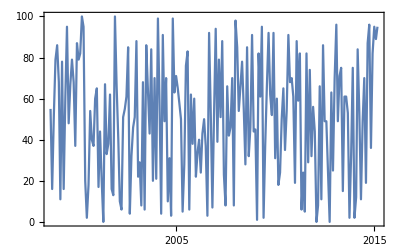

```mathematica
ts1//DateListPlot
```

Multiple time series at once, to produce a rather silly graph:

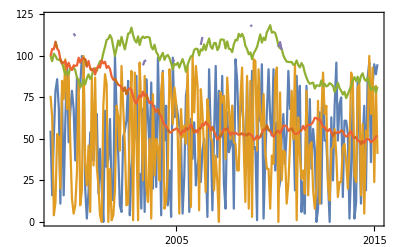

```mathematica
ranges = {"Sheet1","VARIABLE"<>ToString[#]}&/@Range[1,6];
data = importExcelTS["multiple_tests.xlsx",ranges,dropHeaderRows-> 4];
Assert[Dimensions[data]=={6,220,2}];
data // DateListPlot
```

With a non-standard date column. Note the user forgot the dropHeaderRows option, but they were dropped automatically because the first four rows were not valid dates.

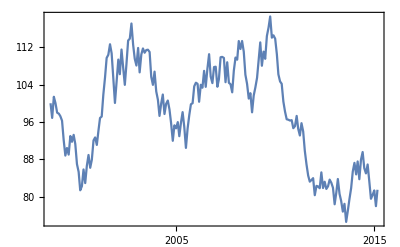

```mathematica
importExcelTS["multiple_tests.xlsx","Sheet4","H:H", dateColumn-> "J"] // DateListPlot
```

## Data Refresh Tests

Variable 7 is saved pointing to an old version of the data. In the original, there is only about a year of data; in the updated version of the source data sheet there are much more data. So we should load different datasets, depending on whether we refresh or not.

```mathematica
orig = importExcel["multiple_tests.xlsx","Sheet1","VARIABLE7", refreshWorkbook-> False];
updated = importExcel["multiple_tests.xlsx","Sheet1","VARIABLE7", refreshWorkbook-> True];
Assert[orig ≠ updated];
Assert[orig⟦20,1⟧==Missing["NA"]];
Assert[NumericQ[updated⟦20,1⟧]]
```

## Speed Tests on Typical Datasets

This dataset was designed to represent a spreadsheet of the size typically used to create graphs in Economics: 7 monthly series, each 18 years in length. Some series have a variety of errors and missing values, which are handled gracefully.

Import the whole sheet:

```mathematica
data=ShowTiming[importExcel["multiple_tests.xlsx",{{"Sheet1"}},dropHeaderRows-> 11]];
```

Imported 1917 cells in 0.858 seconds.

A subset of columns at a time:

```mathematica
data=ShowTiming[importExcel["multiple_tests.xlsx","Sheet1","A:B"]];
Assert[Dimensions[data]=={224,2}]
Assert[And @@ StringQ /@ data⟦1;;4,1⟧]
Assert[And @@ DateListQ /@ data⟦5;;224,1⟧]
Assert[And @@ NumericQ /@ data⟦5;;203,2⟧]
Assert[And @@ (Head[#]==Missing& /@ data⟦204;;224,2⟧)]
```

Imported 448 cells in 0.8424 seconds.

Now, load an entire 5MB XLSX file.

```mathematica
ShowTiming[importExcel["medium_sheet.xlsx",{{"Sheet1"}}]];
```

Imported 399500 cells in 5.4912 seconds.

And a subset of columns from this file :

```mathematica
ShowTiming[importExcel["medium_sheet.xlsx","Sheet1", "B:C"]];
```

Imported 1598 cells in 1.6848 seconds.

## Speed Tests on Large Datasets

This workbook contains a single, large dataset, 500 columns wide, with 10 header rows and 10000 data rows.
First, the 34MB XLSB file (note the built-in Import function does not even support XLSB files).

```mathematica
data = ShowTiming[importExcel["large_sheet.xlsb",{{"Sheet1","B:B"}}]];
Assert[Dimensions[data]=={1,10010,1}];
Assert[And @@ StringQ /@ data⟦1,1;;10,1⟧];
Assert[And @@ NumericQ /@ data⟦1,11;;10010,1⟧];
```

Imported 10010 cells in 3.6348 seconds.

Now, the same tests on the 61MB XLSM file. XLSX files are larger and more complex, and so take longer to parse:

```mathematica
data = ShowTiming[importExcel["large_sheet.xlsm","Sheet1","B:B"]];
Assert[Dimensions[data]=={10010,1}];
Assert[And @@ StringQ /@ data⟦1;;10,1⟧];
Assert[And @@ NumericQ /@ data⟦11;;10010,1⟧];
```

Imported 10010 cells in 14.844 seconds.

Now, how long to import all 5 million cells in the giant sheet?

```mathematica
ShowTiming[importExcel["large_sheet.xlsb",{{"Sheet1"}}]];
```

Imported 5005000 cells in 59.113 seconds.

Same again but for the 61MB XLSM sheet:

```mathematica
ShowTiming[importExcel["large_sheet.xlsm",{{"Sheet1"}}]];
```

Imported 5005000 cells in 63.7998 seconds.

## Invalid Input

Returns $Failed and outputs error messages when the user requests things wrongly. It should be pretty obvious what went wrong, but note that we don’t suppress exceptions raised by Excel here, in case the errors are actually due to something else we didn’t fully anticipate.

```mathematica
importExcel["",{}]
```

importExcel::wrongargs: Wrong arguments.

$Failed

```mathematica
importExcel["foo.xlsx"]
```

importExcel::wrongargs: Wrong arguments.

$Failed

```mathematica
importExcel["multiple_tests.xlsx", {{Symbol}}]
```

importExcel::wrongargs: Wrong arguments.

{$Failed}

Attempting to import a file that does not exist :

```mathematica
importExcel["foo",{{"Sheet1"}}]
```

openWorkbook::nofile: File 'foo' was not found

$Failed

Or if the sheet doesn' t exist.

```mathematica
importExcel["multiple_tests.xlsx",{{"NoSuchSheet"}}]
importExcelTS["multiple_tests.xlsx", {{"NoSuchSheet","B:B"}}]
```

NETLink`NET::netexcptn: A .NET exception occurred: "System.Runtime.InteropServices.COMException (0x8002000B): Invalid index. (Exception from HRESULT: 0x8002000B (DISP_E_BADINDEX))\n   at Microsoft.Office.Interop.Excel.Sheets.get_Item(Object Index)".

importExcel::nosheet: Sheet NoSuchSheet was not found.

{$Failed}

NETLink`NET::netexcptn: A .NET exception occurred: "System.Runtime.InteropServices.COMException (0x8002000B): Invalid index. (Exception from HRESULT: 0x8002000B (DISP_E_BADINDEX))\n   at Microsoft.Office.Interop.Excel.Sheets.get_Item(Object Index)".

importExcelTS::nosheet: Sheet NoSuchSheet was not found.

{$Failed}

Invalid range:

```mathematica
importExcel["multiple_tests.xlsx",{{"Sheet1", "!@#$@#$"}}]
```

NETLink`NET::netexcptn: A .NET exception occurred: "System.Reflection.TargetInvocationException: Exception has been thrown by the target of an invocation. ---> System.Runtime.InteropServices.COMException: Exception from HRESULT: 0x800A03EC\n  ".

importExcel::norange: Range !@#$@#$ was not found.

{$Failed}

```mathematica
importExcelTS["multiple_tests.xlsx","Sheet1","InvalidRange"]
```

NETLink`NET::netexcptn: A .NET exception occurred: "System.Reflection.TargetInvocationException: Exception has been thrown by the target of an invocation. ---> System.Runtime.InteropServices.COMException: Exception from HRESULT: 0x800A03EC\n  ".

importExcelTS::norange: Range InvalidRange was not found.

$Failed

```mathematica
importExcelTS["multiple_tests.xlsx","Sheet1","VARIABLE1", dateColumn-> "Bogus"]
```

importExcelTS::datecolumnletter: Can not identify date column: 'Bogus' is not a valid Excel column identifier. For example, use 'A' to mean the range 'A:A'.

$Failed